## SSA-example.nb

```mathematica
<<xSSA.m
```

xSSA 1.1.α.4 (11-Jul-2009) loaded Sat-11-Jul-2009-16:07:22 using Mathematica 7.0 for Linux x86 (64-bit) (February 18, 2009)(7.0.1)

```mathematica
reactions={{s+e-> se, a}, {se-> s+e, d}, {se-> p+e, k}};
ic = {s-> 100, e-> 25, se-> 0, p-> 0}; 
parms={k-> 1, d-> 1, a-> 1};
```

### "List" option (Default)

```mathematica
sim=SSA[reactions,50,ic,parms];
```

```mathematica
Short[sim, 10]
```

{e→{{0,25},{0.000459739,24},{0.00106745,23},{0.00150865,22},{0.00356889,21},{0.00377175,20},{0.00382852,19},{0.0044245,18},{0.00464908,17},«337»,{4.45527,21},{4.46426,20},{4.67883,21},{5.09992,22},{5.11145,23},{5.13063,22},{5.14082,23},{5.48555,24},{5.53275,25}},«2»,se→{«1»}}

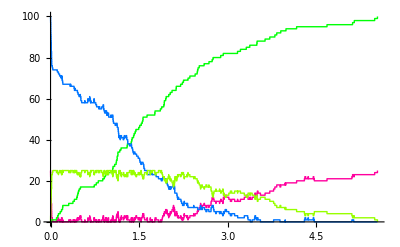

```mathematica
SSAPlot[sim, PlotRange-> All]
```

### "SparseList"

```mathematica
sim=SSA[reactions,50,ic,parms, "Mode"-> "SparseList"];
```

```mathematica
Short[sim, 10]
```

{e→{{0,25},{0.000593694,24},{0.000656955,23},{0.00101777,22},{0.00156835,21},{0.00175858,20},{0.00218953,19},{0.00408817,18},{0.00453823,17},«383»,{5.16862,21},{5.29766,22},{5.33502,21},{5.35682,22},{5.37456,23},{5.49649,22},{5.56097,23},{6.51541,24},{7.24655,25}},«2»,se→{«1»}}

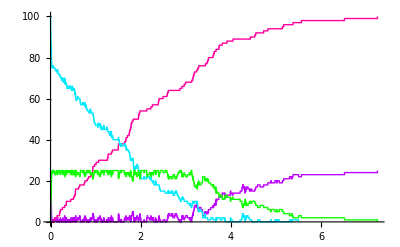

```mathematica
SSAPlot[sim, PlotRange-> All]
```

### "Table"

```mathematica
sim=SSA[reactions,50,ic,parms, "Mode"-> "Table"];
```

```mathematica
Short[sim, 10]
```

{{time,e,p,s,se},{0,25,0,100,0},{0.0000208152,24,0,99,1},{0.00011593,23,0,98,2},{0.000448289,22,0,97,3},{0.00162874,21,0,96,4},{0.00278441,20,0,95,5},{0.00315946,19,0,94,6},«341»,{6.04883,25,99,1,0},{6.06464,24,99,0,1},{7.82405,25,99,1,0},{7.93696,24,99,0,1},{8.02009,25,99,1,0},{8.10621,24,99,0,1},{9.1117,25,100,0,0}}

### "Interpolation"

```mathematica
sim=SSA[reactions,50,ic,parms, "Mode"-> "Interpolation"]
```

{e→InterpolatingFunction[{{0.,7.43678}},<>],p→InterpolatingFunction[{{0.,7.43678}},<>],s→InterpolatingFunction[{{0.,5.82199}},<>],se→InterpolatingFunction[{{0.,7.43678}},<>]}

```mathematica
<<xlr8r.m
```

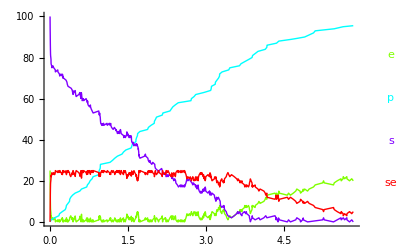

```mathematica
runPlot[sim]
```

### Compare with Deterministic Simulation

```mathematica
dsim=run[SSAtoXLR8R[reactions], rates-> parms, initialConditions-> ic, timeSpan-> 6]
```

{{e→InterpolatingFunction[{{0.,6.}},<>],p→InterpolatingFunction[{{0.,6.}},<>],s→InterpolatingFunction[{{0.,6.}},<>],se→InterpolatingFunction[{{0.,6.}},<>]}}

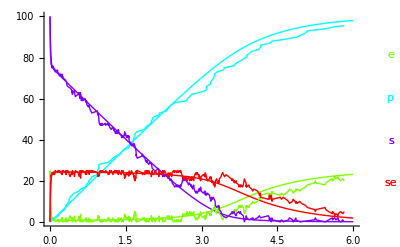

```mathematica
Show[runPlot[dsim], runPlot[sim]]
```